The Langevin function is

```mathematica
L[x_]:=Coth[x]-1/x
```

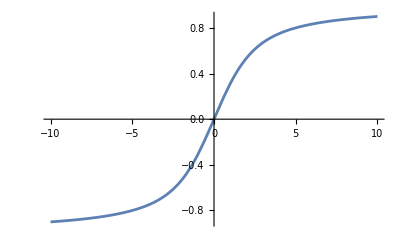

```mathematica
Plot[
L[x],{x,-10,10}
]
```

Giving M in units of M_s and parameter a in units of μ_0, we can solve the Weiss mean field equation:

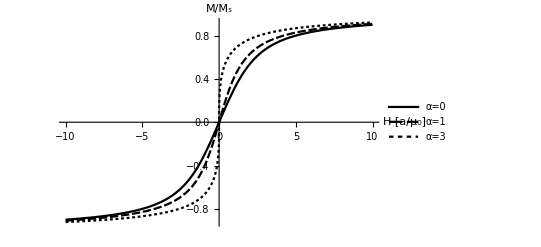

```mathematica
plot=Plot[
{
L[H/a]/.{a->1},
M/.FindRoot[(L[(H+α M)/a]/.{a->1,α->1})-M,{M,1}],
M/.FindRoot[(L[(H+α M)/a]/.{a->1,α->3})-M,{M,1}]
},
{H,-10,10},
PlotLegends->Placed[{"α=0","α=1","α=3"},Top],
PlotTheme->"Monochrome",
AxesLabel->{"H [a/μ_0]","M/M_s"},
BaseStyle->FontSize->16
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["weiss.pdf",plot]
```

/home/jk/temp/thesis/figs/mathematica

weiss.pdf

#### Jiles-Atherton (1986)

Define the Langevin function:

```mathematica
L[x_]:=Coth[x]-1/x
```

Solve for the first curve (ascending in H):

```mathematica
MM0[params_]:=M/.NDSolve[
{( M'[H]==1/(1+c)(Ms L[(H+α M[H])/a]-M[H])/(k-α(Ms L[(H+α M[H])/a]-M[H]))+c/(1+c)(Ms L'[(H+α M[H])/a]((1+α M'[H])/a)-M'[H]))/.params,(M[Hi0+dH]==Mi0)/.params},
M,{H,Hi0+dH,Hf0+dH}/.params]⟦1,1⟧;
```

Define a function to plot a curve:

```mathematica
p[M_,params_]:=Plot[
Evaluate[M[10^3 H]]/(Ms/.params),
{H,M["Domain"]⟦1,1⟧/10^3,M["Domain"]⟦1,2⟧/10^3},
PlotRange->{{M["Domain"]⟦1,1⟧/10^3,M["Domain"]⟦1,2⟧/10^3},{-1,1}},
PlotTheme->"Monochrome",
AxesLabel->{"H [kA/m]","M/M_s"},
BaseStyle->FontSize->16,
PlotStyle->Thickness[0.002]
]
```

Define a function that gives the next curve (changes direction of H change, and reduces the range of H):

```mathematica
MMnext[Mprev_,δ_,params_]:=M/.NDSolve[
{(M'[H]==1/(1+c)(Ms L[(H+α M[H])/a]-M[H])/((-1)^δ k-α(Ms L[(H+α M[H])/a]-M[H]))+c/(1+c)(Ms L'[(H+α M[H])/a]((1+α M'[H])/a)-M'[H]))/.params,M[Mprev["Domain"]⟦1,Mod[δ,2]+1⟧]==Mprev[Mprev["Domain"]⟦1,Mod[δ,2]+1⟧]},
M,{H,Mprev["Domain"]⟦1,Mod[δ,2]+1⟧,(decay*(Mprev["Domain"]⟦1,Mod[δ+1,2]+1⟧-dH)+dH)/.params}
]⟦1,1⟧;
```

Repeat the degaussing for N times:

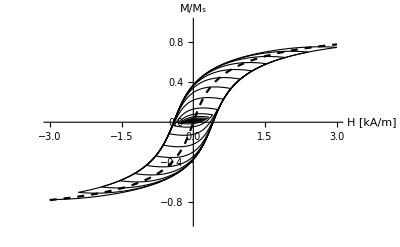
-Graphics-ΔH=0, Ms=1.6e6, c=0.2, a=1100, α=1.6e-3, k=400

```mathematica
params={Hi0->-3000,Hf0->3000,dH->0,Mi0->-1.24 10^6,Ms->1.6 10^6,c->.2,a->1100,α->1.6 10^-3,k->400,decay->0.8};
Ntimes=30;

Marr = NestList[
{MMnext[#⟦1⟧,#⟦2⟧+1,params],#⟦2⟧+1,params}&,
{MM0[params],0,params},Ntimes];

weiss=Plot[
 (M/Ms/.params)/.FindRoot[(Ms L[(H 10^3+α M)/a]/.params)-M,{M,1000}],
{H,Hi0/10^3,Hf0/10^3}/.params,
PlotStyle->{Black,Dashed}
];

plot2=Labeled[
Show[Table[p[x⟦1⟧,params],{x,Marr}],weiss],
"ΔH=0, Ms=1.6e6, c=0.2, a=1100, α=1.6e-3, k=400",Top,LabelStyle->{FontSize->14,FontFamily->"Helvetica"}
]

(*SetDirectory[NotebookDirectory[]];
Export["jiles_atherton.pdf",plot2];*)
```

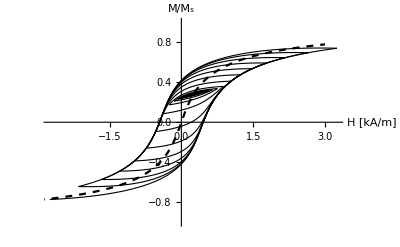
-Graphics-ΔH=250, Ms=1.6e6, c=1.2, a=1100, α=1.6e-3, k=400

```mathematica
params={Hi0->-3000,Hf0->3000,dH->250,Mi0->-1.24 10^6,Ms->1.6 10^6,c->1.2,a->1100,α->1.6 10^-3,k->400,decay->0.8};
Ntimes=30;

Marr = NestList[
{MMnext[#⟦1⟧,#⟦2⟧+1,params],#⟦2⟧+1,params}&,
{MM0[params],0,params},Ntimes];

weiss=Plot[
 (M/Ms/.params)/.FindRoot[(Ms L[(H 10^3+α M)/a]/.params)-M,{M,1000}],
{H,Hi0/10^3,Hf0/10^3}/.params,
PlotStyle->{Black,Dashed}
];

plot2=Labeled[
Show[Table[p[x⟦1⟧,params],{x,Marr}],weiss],
"ΔH=250, Ms=1.6e6, c=1.2, a=1100, α=1.6e-3, k=400",Top,LabelStyle->{FontSize->14,FontFamily->"Helvetica"}
]

(*SetDirectory[NotebookDirectory[]];
Export["jiles_atherton_offs.pdf",plot2];*)
```